```mathematica
(****
TEMPLATE FOR ITERATIVE OPTIMIZATION ALGORITHMS
Zicheng Gao
 ****)
```

```mathematica
(*** Iteration Settings ***)
InitIterationSettings[]:=(
(* Controls - zero fps means that there is NO DELAY *)
doPrint=False;
doPoint=True;
doGraph=False;
doWarn=False;
doPlot=True;
doSpace=True;
doEPlot=True;

showMistakes=False;
fps=0;

(** Adaptivity **)
errorRatio=1.0;(*In what ratio of current error to previous error should it be considered increasing*)
boostRatio=1.1; (*'Impatience' Multiplier to increase factor when error is not increasing*)
refineRatio=0.95;(*'Caution' Multiplier to decrease factor when error is increasing*)
maxRefines=1000;(*Give up refining if refined too many times in a row*)

(* Acceleration *)
AccelBoost=1.;
AccelRefine=1.;
AccelAmt=0.01;

(* Tracker values *)
historyAmt=300;

(*Display*)
GradientPerf="Speed";
dispGradientRange=1.;
);
InitIterationSettings[];
```

```mathematica
InitFunctionData[paramVariance_,manualTrueParams_,noiseFactor_, noiseDistribution_,forceData_,arbitfunc_]:=(
Clear[eFunc,gFunc,params];
ParamVariance=paramVariance;

(*If we are forcing data, use data, otherwise generate data*)
If[Length[forceData]>0,
Data=forceData;
DataLength=Length[Data];
SamplingSet=N@Range@DataLength/N@SamplingRate;
(* Else *),
SamplingSet=N@Range@DataLength/N@SamplingRate;
TrueParams=If[Length[manualTrueParams]>0,manualTrueParams,RandomReal[{-paramVariance,paramVariance},varamt]];
(* Data Generation *)
NoiselessData=((Fitfunction@@ #&)/@(Prepend[TrueParams, #]& /@SamplingSet));
AddNoise=(#+noiseFactor*RandomVariate[noiseDistribution])&;
Data=AddNoise/@NoiselessData;
];
(*Prep gradient*)
params=Table[Unique["p"],{varamt}];paramh=Hold@@params;

(* Objective and Gradient functions if there is no arbitrary minimizing function, of course *)
doArbitraryFitting=(arbitfunc=!={});
If[doArbitraryFitting,
eFunc=N@arbitfunc,
eFunc=paramh/._[vars__]:>Function[{vars},N[Mean[(((Fitfunction@@Prepend[{vars},#])&/@SamplingSet)-Data)^2]]]];
gFunc=paramh/._[vars__]:>Function[{vars},Evaluate@Grad[eFunc@@params,params]];
);
(*** Global Iteration Reset / Initialize ***)
InitIterationData[factorx_,manualParams_]:=(
totalIter=0;
TotalRefines=0;
factor=factorx;
dirs=ConstantArray[ConstantArray[0,varamt],Smoothness];
dirX=0;
ConsecRefines=0;
(*History*)
iterParams=initParams=If[Length[manualParams]>0,manualParams,RandomReal[{-ParamVariance,ParamVariance},varamt]];
debugParams={iterParams};
err=eFunc@@iterParams;
prevErr=err+1.;
dir=gFunc@@iterParams;
debugErr={err};
);
LinePlot[points_, size_,amount_]:=Show[
ListPointPlot3D[
{If[amount>0&&size>amount,points[[-amount;;-1]],points]},
PlotRange->All,ImageSize->Medium],
Graphics3D@Line@points
];
ReportIteration[i_]:=If[Mod[i,100]==0 && doPrint,Print["next dir:",dir,"\nerr:",err,"\nparams:",iterParams,"\niteration:",i];];
(* Realtime monitor plot *)
displayGradient[xV_,yV_]:=Show[
ContourPlot[eFunc @@ ReplacePart[iterParams, {xV->x,yV->y}],
{x,iterParams[[xV]]-dispGradientRange,iterParams[[xV]]+dispGradientRange},{y,iterParams[[yV]]-dispGradientRange,iterParams[[yV]]+dispGradientRange},
PlotTheme->"Web",AxesLabel->{x,y,z},PlotRange->All,ImageSize->Small,PerformanceGoal->GradientPerf
],
Graphics[{
Blue,PointSize[0.05],Point[{iterParams[[xV]],iterParams[[yV]]}],
Arrow[{{iterParams[[xV]],iterParams[[yV]]},{iterParams[[xV]]-factor*dir[[xV]],iterParams[[yV]]-factor*dir[[yV]]}}]
}]
];
(* Realtime monitor plot *)
displayGradientNorm[xV_,yV_,ϵ_]:=Show[
ContourPlot[Norm[gFunc @@ ReplacePart[iterParams, {xV->x,yV->y}]],
{x,iterParams[[xV]]-dispGradientRange,iterParams[[xV]]+dispGradientRange},{y,iterParams[[yV]]-dispGradientRange,iterParams[[yV]]+dispGradientRange},
RegionFunction->Function[{x,y,z},z≤ϵ], PlotTheme->"Web",AxesLabel->{x,y,z},PlotRange->All,ImageSize->Small,PerformanceGoal->GradientPerf
],
Graphics[{
Blue,PointSize[0.05],Point[{iterParams[[xV]],iterParams[[yV]]}],
Arrow[{{iterParams[[xV]],iterParams[[yV]]},{iterParams[[xV]]-factor*dir[[xV]],iterParams[[yV]]-factor*dir[[yV]]}}]
}]
];
Visualize[]:=
Dynamic@Grid[{
{"Data vs Function","Parameter Space","Error over iterations"},
{
If[doArbitraryFitting,"Arbitrary Optimization",ListPlot[{(Fitfunction@@Prepend[iterParams,#])&/@SamplingSet,Data},Joined->True,ImageSize->Medium,PlotLegends->None]],
If[doPoint,
Which[
varamt==3,LinePlot[debugParams,totalIter,historyAmt],
varamt==2,Show[
Plot3D[eFunc[x,y],{x,-3,3},{y,-3,3},
Mesh->None],
Graphics3D@Line@({Append[#,eFunc@@#]&}/@debugParams)
],
True,"Incorrect dimensionality"
],
"Disabled"],
If[doEPlot,ListLogLogPlot[debugErr,ImageSize->Medium,PlotRange->All],"Disabled"]
},
{"Parameters, nGrad, dir, Delta","Iterations, factor, corrections"},
{
Column[{iterParams,-dir,-factor*dir,-factor*SmoothingFunction[dirs]}],
Column[{{totalIter,factor,TotalRefines},ProgressIndicator[ConsecRefines/maxRefines]}],
{(Total[(((Fitfunction@@Prepend[iterParams,#])&/@SamplingSet)-Data)^2]/(DataLength-varamt))^0.5,prevErr}
}
},
Frame->All,ItemSize->30
];
RefineFactor[]:=(factor*=refineRatio^AccelRefine;ConsecRefines++;TotalRefines++;AccelRefine+=AccelAmt;AccelBoost=1.;);
BoostFactor[]:=(factor*=boostRatio^AccelBoost;prevErr=err;ConsecRefines=0;AccelBoost+=AccelAmt;AccelRefine=1.;);
AddToHistory[]:=(debugParams=Append[debugParams,iterParams];debugErr=Append[debugErr,err];);
ToSpacedString=Function[str,StringDrop[StringJoin@@((ToString[#]<>" ")&/@str),-1]];
FindMax[list_]:=Position[list,Max@list][[1,1]];
RecoverFrequency[data_,len_,rate_]:=N[(#-2+2(FindMax@Abs@Fourier[data*Exp[2I π(#-2)N@(Range@len-1)/len],FourierParameters->{0,2/len}]-1)/len)*2π*rate/len]&@FindMax@Abs@Fourier@data;
```

```mathematica
RecordedComparisonData={};
```

```mathematica
(* SET DATA *)
varamt=3;
DataLength=100;
SamplingRate=100;
Fitfunction=Exp[#1]Sin[#1*#2]&;
InitFunctionData[10.,{9.03091,6.9648},0.,NormalDistribution[],{},
#1(1.-#2)^2/#1+100.(#3-#2^2)^2&
];
```

```mathematica
(* BEGIN ITERATION *)
InitIterationSettings[];
Smoothness=6;
showMistakes=True;
SmoothingFunction[l_]:=Total[MapIndexed[#1 /2.^First[#2]&,l]]/Smoothness;
InitIterationData[0.01,{}];
recordAtIter=200;
Visualize[]
```

```mathematica
(*** Iteration loop ***)

(* Iterator and maximum values *)
i=0.;UpperBound=1000.;
SmallErr=0.0000000000000001;
NoErr=True;
Forever=False;
(* Iteration *)
While[ConsecRefines<maxRefines&&(Forever||(i<UpperBound &&(NoErr|| ((err(err-prevErr))^2+1)^2>(1+SmallErr)))),
(* Obtain vector from gradient and assign into running array *)
dirs=Prepend[Drop[dirs,-1],dir=gFunc@@iterParams];
ReportIteration[i];(*Report*)If[fps≠0&&ConsecRefines==0,Pause[fps];];(*Pause*)
If[showMistakes,AddToHistory[];];
(*Mark down boost vs error - please do not change other variables*)
iterParams-=factor*SmoothingFunction[dirs];
If[ConsecRefines==0,i++;totalIter++;];
err=eFunc @@ iterParams;
(* Factor Adaptivity - check to see whether error has increased over errorRatio to determine whether to boost or refine *)
If[err/prevErr>errorRatio,
(*If err increased, revert, refine, and retry*)
iterParams=debugParams[[-1]];If[Log10[factor]<-100,factor=0.5];
RefineFactor[];,AddToHistory[];BoostFactor[];];
]
```

```mathematica
(** Data Recording **)
RecordedComparisonData=Catenate[{
RecordedComparisonData,
{{
{"Smoothness",Smoothness},
debugErr,
debugParams,
TotalRefines,
{"BoostRatio",boostRatio},
{"RefineRatio",refineRatio}
}}
}];
```

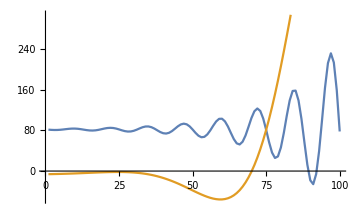

```mathematica
(***Diagnostic Tools***)

(*Parameter History*)
Grid[debugParams[[-10;;-1]]];
Column[eFunc @@ #&/@ debugParams[[-10;;-1]]];
Grid[gFunc @@ #&/@ debugParams[[-10;;-1]]];

(*"Best Parameters" Generated with NMinimize*)
AutoParams=params/.NMinimize[eFunc @@ params,params][[2]];

(*Compare current data, auto-fitted data, and generated data*)
ListPlot[{
(*(Fitfunction@@Prepend[iterParams,#])&/@SamplingSet,*)
(Fitfunction@@Prepend[AutoParams,#])&/@SamplingSet,
Data},Joined->True,ImageSize->Medium]
```

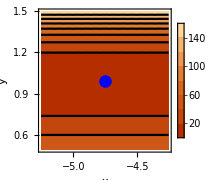

```mathematica
dispGradientRange=0.5;
dispGradientThresh=1.5;
GradientPerf="Performance";
Which[
varamt==3,
{displayGradient[1,2],displayGradient[2,3],displayGradient[3,1]};
{displayGradientNorm[1,2,dispGradientThresh],displayGradientNorm[2,3,dispGradientThresh],displayGradientNorm[3,1,dispGradientThresh]};,
varamt==2,
displayGradient[1,2];
displayGradientNorm[1,2,dispGradientThresh]
]
displayGradient[1,2]
```

```mathematica
LinePlot[debugParams,Length@debugParams,Length@debugParams]
```

-Graphics3D-

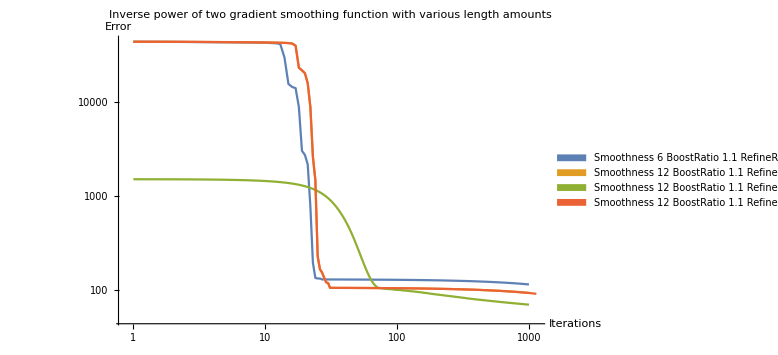

```mathematica
ListLogLogPlot[
Table[RecordedComparisonData[[sm,2]],{sm,1,Length@RecordedComparisonData}],PlotLegends->SwatchLegend[
Table[
Column[
Join[
Flatten@ToSpacedString/@RecordedComparisonData[[sm,{1,5,6,7,8}]],
{ToSpacedString@{"Final error:",Last@RecordedComparisonData[[sm,2]]}}
]
],{sm,1,Length@RecordedComparisonData}],
LegendFunction->"Panel"],
PlotLabel->"Inverse power of two gradient smoothing function with various length amounts",
AxesLabel->{"Iterations","Error"},
PlotRange->All,
ImageSize->Large,
Joined->True]
```

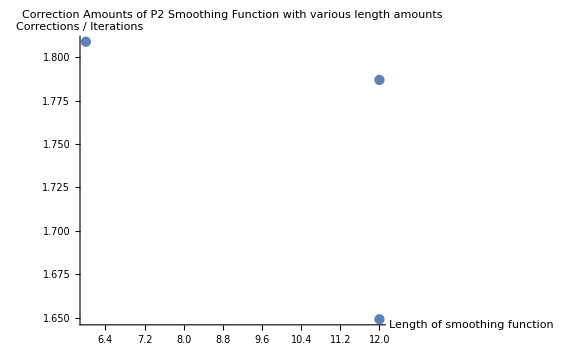

```mathematica
ListPlot[
Table[{RecordedComparisonData[[sm,1,2]],RecordedComparisonData[[sm,4]]/1000.},{sm,1,Length@RecordedComparisonData}],
AxesLabel->{"Length of smoothing function","Corrections / Iterations"},
PlotLabel->"Correction Amounts of P2 Smoothing Function with various length amounts",
ImageSize->Large
]
```

```mathematica
Data
TrueParams
```

{-0.0110631,-0.0108652,-0.010643,-0.0103958,-0.0101234,-0.00982587,-0.00950351,-0.00915714,-0.008788,-0.00839783,-0.00798893,-0.00756421,-0.0071272,-0.00668218,-0.00623414,-0.00578889,-0.00535304,-0.00493409,-0.00454038,-0.0041812,-0.00386669,-0.00360793,-0.00341686,-0.00330625,-0.00328967,-0.00338142,-0.00359639,-0.00395002,-0.00445809,-0.00513661,-0.0060016,-0.00706885,-0.00835374,-0.00987087,-0.0116338,-0.0136547,-0.015944,-0.0185098,-0.0213577,-0.0244902,-0.0279061,-0.0316002,-0.0355626,-0.0397781,-0.0442257,-0.0488783,-0.0537014,-0.0586535,-0.0636848,-0.0687368,-0.0737423,-0.0786247,-0.0832973,-0.0876637,-0.0916173,-0.0950412,-0.0978086,-0.0997828,-0.100818,-0.100758,-0.0994419,-0.0966993,-0.0923554,-0.0862313,-0.0781464,-0.0679203,-0.0553755,-0.0403405,-0.0226525,-0.00216168,0.0212653,0.0477406,0.0773509,0.110152,0.146163,0.185362,0.22768,0.272991,0.321113,0.371794,0.42471,0.479458,0.535547,0.592398,0.64933,0.705563,0.760208,0.812266,0.860623,0.904055,0.941217,0.970656,0.990807,1.,0.996469,0.978363,0.943754,0.890659,0.817055,0.720903}

{9.03091,6.9648,-6.23602}

```mathematica
eFunc
gFunc
```

(1.-1. #2)^2+100. (-1. #2^2+#3)^2&

Function[{p28,p29},{0,-2. (1.-1. p29)-400. p29 (-1. p29^2+#3)}]